```mathematica
Table[{Prime[i+1]-Prime[i],2*PrimePi@Sqrt@Prime[i+1]},{i,300}];
Do[If[(g=Prime[i+1]-Prime[i])>(arrow=2*PrimePi@Sqrt@Prime[i+1]),Print[{i,g,arrow}]],{i,30000}]
```

{1,1,0}

{30,14,10}

{217,34,22}

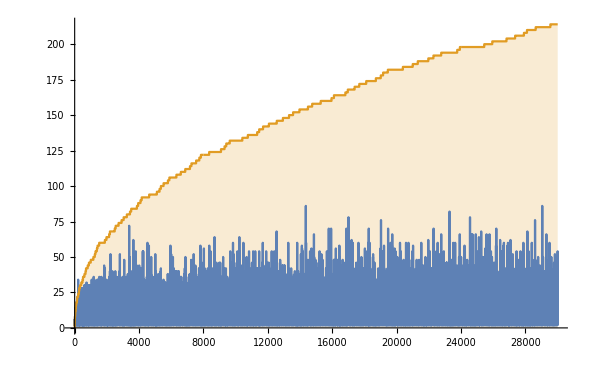

```mathematica
DiscretePlot[{Prime[i+1]-Prime[i],2*PrimePi@Sqrt@Prime[i+1]},{i,30000}]
```

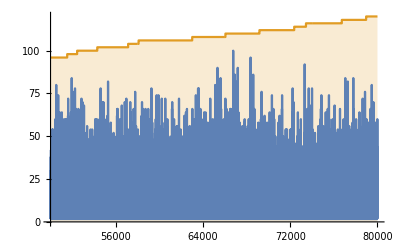

```mathematica
DiscretePlot[{Prime[i+1]-Prime[i],2*PrimePi@Sqrt@i},{i,50000,80000}]
```

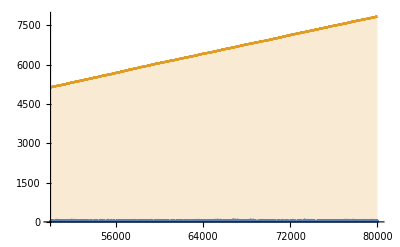

```mathematica
DiscretePlot[{Prime[i+1]-Prime[i],PrimePi@i},{i,50000,80000}]
```